```mathematica
st190333$line=Range[-20,20]
```

{-20,-19,-18,-17,-16,-15,-14,-13,-12,-11,-10,-9,-8,-7,-6,-5,-4,-3,-2,-1,0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

```mathematica
st190333$list=st190333$line^2
```

{400,361,324,289,256,225,196,169,144,121,100,81,64,49,36,25,16,9,4,1,0,1,4,9,16,25,36,49,64,81,100,121,144,169,196,225,256,289,324,361,400}

## ListPlot

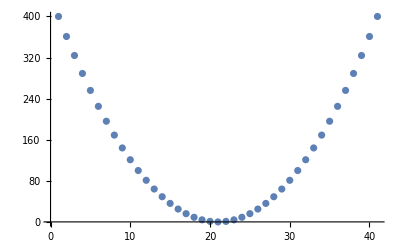

```mathematica
ListPlot[st190333$list]
```

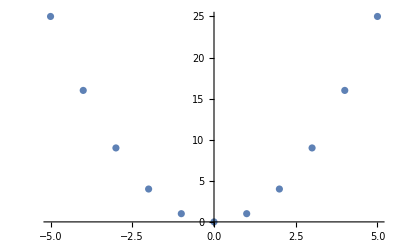

```mathematica
ListPlot[{{-5,25},{-4,16}, {-3,9}, {-2,4},{-1,1},{0,0},{1,1},{2,4},{3,9},{4,16},{5,25}}]
```

## ListLinePlot

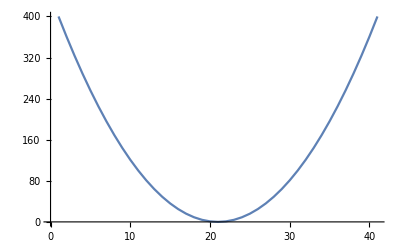

```mathematica
ListLinePlot[st190333$list]
```

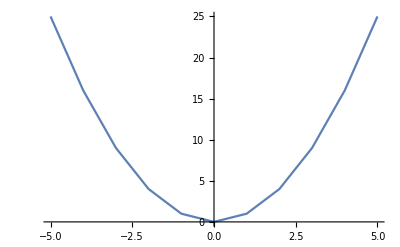

```mathematica
ListLinePlot[{{-5,25},{-4,16}, {-3,9}, {-2,4},{-1,1},{0,0},{1,1},{2,4},{3,9},{4,16},{5,25}}]
```

## ListStepPlot

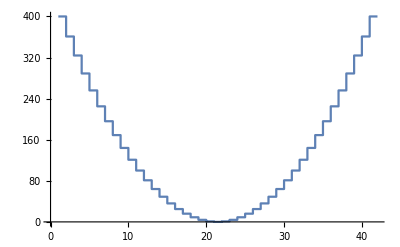

```mathematica
ListStepPlot[st190333$list]
```

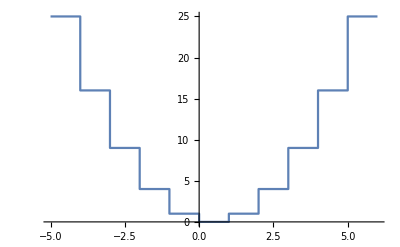

```mathematica
ListStepPlot[{{-5,25},{-4,16}, {-3,9}, {-2,4},{-1,1},{0,0},{1,1},{2,4},{3,9},{4,16},{5,25}}]
```

## StackedListPlot

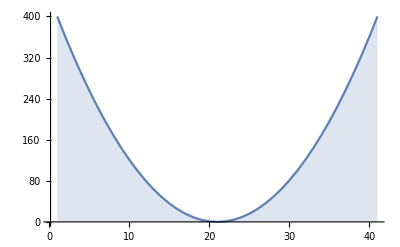

```mathematica
StackedListPlot[st190333$list]
```

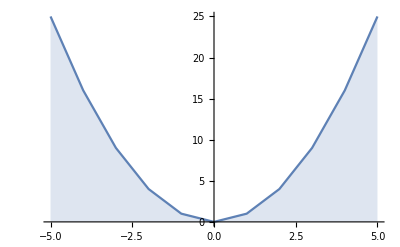

```mathematica
StackedListPlot[{{-5,25},{-4,16}, {-3,9}, {-2,4},{-1,1},{0,0},{1,1},{2,4},{3,9},{4,16},{5,25}}]
```

## ListLogPlot

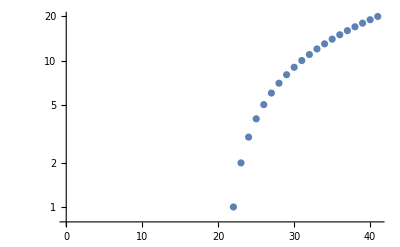

```mathematica
ListLogPlot[st190333$line]
```

## ListLogLinearPlot

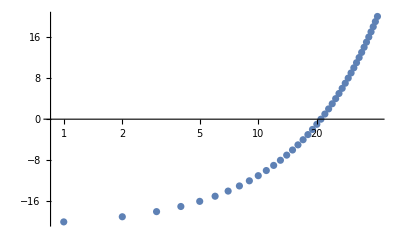

```mathematica
ListLogLinearPlot[st190333$line]
```

## ListLogLogPlot

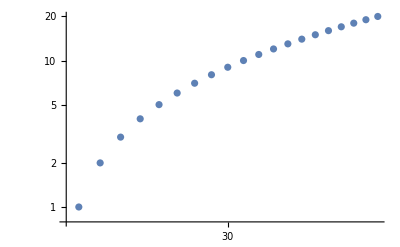

```mathematica
ListLogLogPlot[st190333$line]
```

## ListPolarPlot

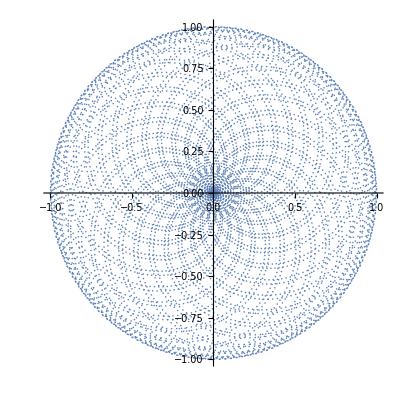

```mathematica
ListPolarPlot[Sin[Range[8000]]]
```

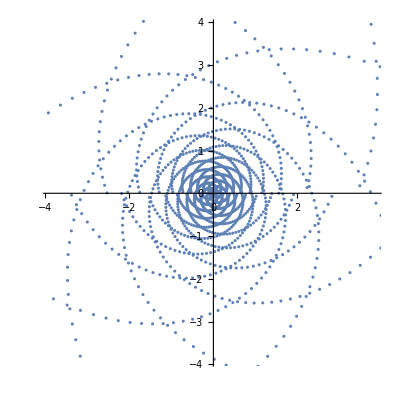

```mathematica
ListPolarPlot[Tan[Range[2000]]]
```

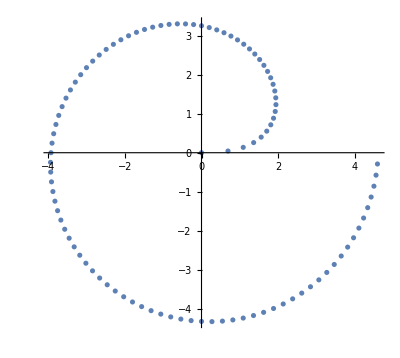

```mathematica
ListPolarPlot[Log[Range[100]]]
```

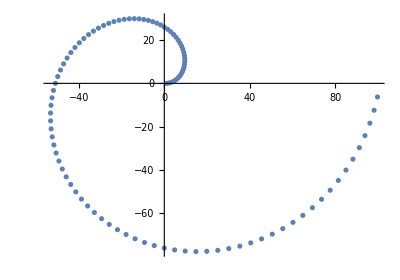

```mathematica
ListPolarPlot[Range[100]]
```

### ListPlot3D

```mathematica
ListPlot3D[{{1,0,0}, {0,1,0},{0,0,1}}]
```

-Graphics3D-

## ListPointPlot3D

```mathematica
ListPointPlot3D[{{1,0,0}, {0,1,0},{0,0,1}}]
```

-Graphics3D-

## ListLinePlot3D

```mathematica
ListLinePlot3D[{{1,0,0}, {0,1,0},{0,0,1}}]
```

-Graphics3D-

## ListDensityPlot

```mathematica
ListDensityPlot[{{1,0,0}, {0,1,0},{0,0,1}}]
```

-Graphics-

## ListContourPlot

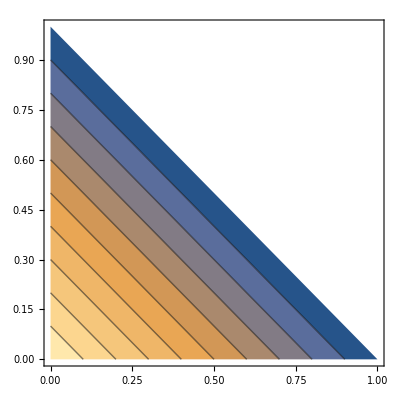

```mathematica
ListContourPlot[{{1,0,0}, {0,1,0},{0,0,1}}]
```

## ArrayPlot

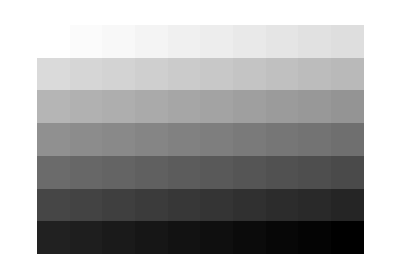

```mathematica
ArrayPlot[
{
Range[0,9],
Range[10,19],
Range[20,29],
Range[30,39],
Range[40,49],
Range[50,59],
Range[60,69]
}
]
```

## MatrixPlot

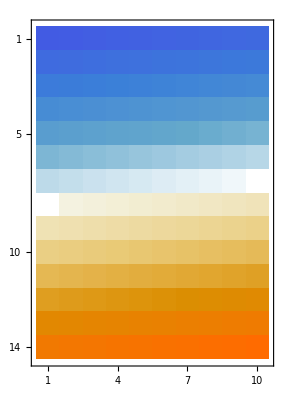

```mathematica
MatrixPlot[
{
Range[-69,-60],
Range[-59,-50],
Range[-49,-40],
Range[-39,-30],
Range[-29,-20],
Range[-19,-10],
Range[-9,-0],
Range[0,9],
Range[10,19],
Range[20,29],
Range[30,39],
Range[40,49],
Range[50,59],
Range[60,69]
}
]
```

## ArrayPlot3D

```mathematica
ArrayPlot3D[{
{{1,2,3}, {2,2,2}, {3,3,3}},
{{1,1,1}, {2,2,2}, {3,3,3}},
{{4,4,4}, {4,4,4}, {4,4,4}},
{{5,5,5}, {5,5,5}, {5,5,5.}}
}]
```

-Graphics3D-

## RadialAxisPlot

```mathematica
RadialAxisPlot[{1,1,1,1,1,1,1}]
```

-Graphics-

## Date & Time Visualization

### DateListPlot

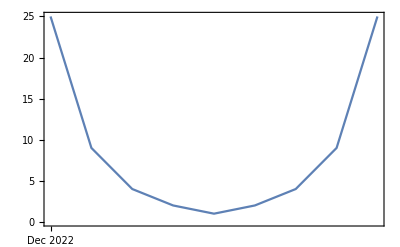

```mathematica
DateListPlot[
{25,9,4,2,1,2,4,9,25},
{2022,12,1}
]
```

### DateListLogPlot

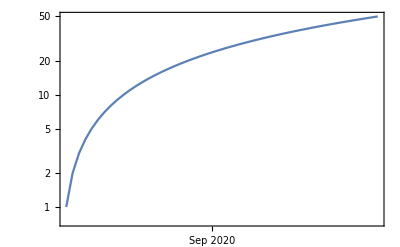

```mathematica
DateListLogPlot[Range[50], {2020,08,09}]
```

### TimelinePlot

```mathematica
TimelinePlot[
{
{
DateInterval[{{2021,12,22},{2022,01,11}}],
DateInterval[{{2022,05,18},{2022,06,07}}],
DateInterval[{{2022,12,22},{2023,01,11}}]
},
{
DateInterval[{{2021,09,01},{2021,12,21}}],
DateInterval[{{2022,01,26},{2022,05,17}}],
DateInterval[{{2022,09,01},{2022,12,21}}]
}
},
Filling->Bottom
]
```

-Graphics-

## Graph Visualization

### GraphPlot

```mathematica
GraphPlot[{
Labeled["1"->"2","10"],
Labeled["1"->"3","15"],
Labeled["2"->"4","20"],
Labeled["2"->"3","0"],
Labeled["3"->"4","20"],
Labeled["3"->"5","15"],
Labeled["4"->"6","6"],
Labeled["4"->"5","6"],
Labeled["5"->"7","15"],
Labeled["6"->"7", "10"]
},
PlotTheme->"DiagramGreen"
]
```

-Graphics-

### LayeredGraphPlot

```mathematica
LayeredGraphPlot[{
Labeled["1"->"2","10"],
Labeled["1"->"3","15"],
Labeled["2"->"4","20"],
Labeled["2"->"3","0"],
Labeled["3"->"4","20"],
Labeled["3"->"5","15"],
Labeled["4"->"6","6"],
Labeled["4"->"5","6"],
Labeled["5"->"7","15"],
Labeled["6"->"7", "10"]
},
PlotTheme->"DiagramGreen"
]
```

-Graphics-

### TreePlot

```mathematica
TreePlot[{
Labeled["1"->"2","12"],
Labeled["1"->"3","3"],
Labeled["1"->"4","4"],
Labeled["2"->"5","2"],
Labeled["2"->"6","2"],
Labeled["3"->"7","9"],
Labeled["3"->"8","8"],
Labeled["4"->"9","7"],
Labeled["4"->"10","6"],
Labeled["4"->"11", "3"],
Labeled["5"->"12","3"],
Labeled["5"->"13", "3"]
},
PlotTheme->"DiagramGreen"
]
```

-Graphics-

## Charting & Information Visualization

### BarChart

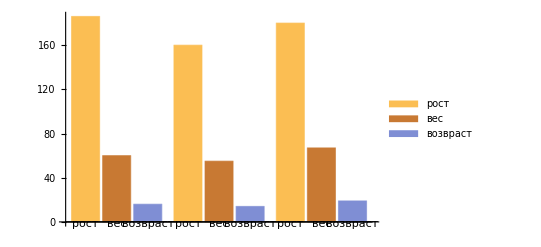

```mathematica
BarChart[{{186,60,16},{160,55,14},{180,67,19}}, ChartLabels->{"рост","вес","возвраст"},ChartLegends->{"рост","вес","возвраст"}]
```

### PieChart

```mathematica
PieChart[{4,20,3,21}, ChartLegends->{"девочки ПО-4", "мальчики ПО-4","девочки ПО-5", "мальчики ПО-5"}, ChartStyle->"DarkRainbow"]
PieChart[{{4,20},{3,21}}, ChartLegends->{"девочки", "мальчики"}, ChartStyle->"DarkRainbow"]
```

-Graphics-

-Graphics-

### BarChart3D

```mathematica
BarChart3D[{{186,60,16},{160,55,14},{180,67,19}},ChartStyle->"DarkRainbow",ChartLegends->{"рост","вес","возвраст"}]
```

-Graphics3D-

### PieChart3D

```mathematica
PieChart3D[{4,20,3,21}, ChartLegends->{"девочки ПО-4", "мальчики ПО-4","девочки ПО-5", "мальчики ПО-5"}, ChartStyle->"DarkRainbow"]
PieChart3D[{{4,20},{3,21}}, ChartLegends->{"девочки", "мальчики"}, ChartStyle->"DarkRainbow"]
```

-Graphics3D-

-Graphics3D-

## Anatomy Visualization

### AnatomyPlot3D

```mathematica
AnatomyPlot3D[{Entity["AnatomicalStructure","Brain"]}]
```

-Graphics3D-